# CKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Stable and usntable manifolds

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Symmetry lines

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=84/100;
τ=1;
```

```mathematica
line=Table[{Rationalize[i],0},{i,0,1.999,0.00005}];
sym=ParallelTable[rot[α/2].i,{i,line}];
symb=Table[rot[Pi/2].i,{i,sym}];
```

```mathematica
sym//Length
```

39981

```mathematica
ListPlot[{sym,symb},AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.9999],1000];
```

```mathematica
k=4.0;
```

```mathematica
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincare=Graphics[{PointSize[0.0015],Gray,Opacity[0.4],Point[newpoincarea]},PlotRange->{{0,2.1},{0,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
```

```mathematica
n=5;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,sym}];
newpoincarea=ArrayReshape[puntosa,{Length[sym]*(n+1),2}];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[1],Point[newpoincarea]},PlotRange->{{0,2.1},{0,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,symb}];
newpoincarea=ArrayReshape[puntosa,{Length[sym]*(n+1),2}];
symmetriesb=Graphics[{PointSize[0.0015],Blue,Opacity[1],Point[newpoincarea]},PlotRange->{{0,2.1},{0,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];

Export["symmetry_b_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>".png",Show[{symmetries,symmetriesb,poincare}]];
```

## Manifolds

The guess is that for α = π/2 and k = 5.0, there is an unstable periodic point at (Q,P) = (1,1) with stable and unstable manifolds as straight lines going only to the +Q and +P axis.

```mathematica
Clear[Jx,Jy,Jz];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];
(*Jacobian*)
Clear[M];
M[Jini_,α_,k_]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}
];
(*Clear[M];
M[{x_,y_,z_},α_,k_]:=Module[{M},
M={{∂_x Jx[x,y,z,α,k],∂_y Jx[x,y,z,α,k],∂_z Jx[x,y,z,α,k]},
{∂_x Jy[x,y,z,α,k],∂_y Jy[x,y,z,α,k],∂_z Jy[x,y,z,α,k]},{∂_x Jz[x,y,z,α,k],∂_y Jz[x,y,z,α,k],∂_z Jz[x,y,z,α,k]}}
];*)
```

```mathematica
{qini,pini}={1,1};
```

```mathematica
{xini,yini,zini}=change2[{qini,pini}]
```

{1/(√2),1/(√2),0}

```mathematica
α=Pi/2;
k=5;
```

```mathematica
mapeo[{qini,pini},α,k,2]//N
```

{{1.,1.},{0.818934,0.886865},{1.14977,1.02129}}

```mathematica
(*It's not fixed point*)
```

```mathematica
J=M[{xini,yini,zini},α,k];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[J]]]];
```

```mathematica
eigenval//N
```

{-2.49001,-0.537548,0.747105}

```mathematica
eigenvec//N
```

{{0.503638,-0.202264,1.},{-0.151275,0.281417,1.},{-0.442111,-0.591765,1.}}

```mathematica
δ=10^-4;
perturb=Normalize[{xini,yini,zini}+δ*eigenvec[[1]]];
qpperturb=change[perturb];
kicks=1000;
manifold=mapeo[N[qpperturb],α,k,kicks];
```

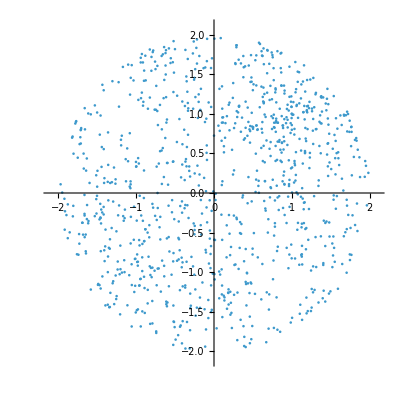

```mathematica
ListPlot[manifold,PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1]
```